# Solving the Keplar Problem

```mathematica
Remove["Global`*"]
```

## Runge Lenz Vector

```mathematica
r[θ_]:=1/(m*k/L^2*(1+A/m/k*Cos[θ]))
```

```mathematica
drdt[θi_]:=D[r[θ],θ]*L/m/r[θi]^2/.{θ->θi}
```

```mathematica
Solve[D[r[θ],θ]==0,θ]
r[0]
r[π]
```

{{θ→ConditionalExpression[2 π C[1],C[1]∈Integers]},{θ→ConditionalExpression[π+2 π C[1],C[1]∈Integers]}}

L^2/(k (1+A/(k m)) m)

L^2/(k (1-A/(k m)) m)

```mathematica
drdt[θ]
```

(A Sin[θ])/(L m)

```mathematica
rA=69816900000;
rP=46001200000;
mM=3.3011*10^(23);
kM=GN*mM*mS;
GN=6.67*10^(-11);
mS=1.98855*10^(30);
```

```mathematica
sols=Solve[r[0]==rP&&r[π]==rA,{L,A}]/.{k->kM,m->mM}
```

{{L→-8.95327×10^38,A→2.97212×10^66},{L→8.95327×10^38,A→2.97212×10^66}}

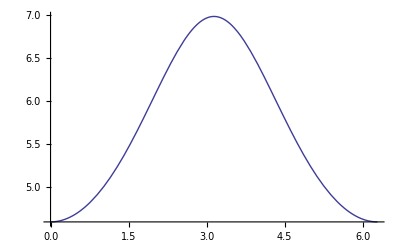

{(5.54604 Cos[θ])/(1+0.20563 Cos[θ]),(5.54604 Sin[θ])/(1+0.20563 Cos[θ])}

```mathematica
Plot[(r[θ]/.sols[[2]]/.{k->kM,m->mM})/10^10,{θ,0,2*π}]
xyM[θ_]:=({r[θ]*Cos[θ],r[θ]*Sin[θ]}/.sols[[2]]/.{k->kM,m->mM})/10^10
xyM[θ]
```

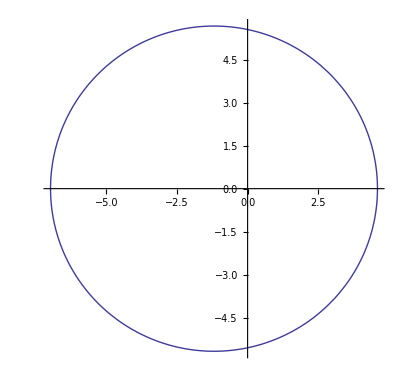

```mathematica
ParametricPlot[xyM[θ],{θ,0,2*π}]
```

```mathematica
sols
```

{{L→-8.95327×10^38,A→2.97212×10^66},{L→8.95327×10^38,A→2.97212×10^66}}

```mathematica
sols[[2,1,2]]/mM
```

2.71221×10^15

```mathematica
(c^2/2*rS/.{c->2.99*10^8,rS->3*10^3})/10^10/(24*60*60)^2
```

1.79641

```mathematica
L =m/2D[r[t],{t}]^2-A/r[t]^1-B/r[t]^2
```

-B/r[t]^2-A/r[t]+1/2 m r'[t]^2

```mathematica
DEQ=D[L,r[t]]-D[D[L,D[r[t],t]],t]==0
```

(2 B)/r[t]^3+A/r[t]^2-m r''[t]==0

```mathematica
DSolve[DEQ/.{B->0},r[t],t]
```

Solve[((A Log[A-m C[1] r[t]-m √C[1] √(C[1]-(2 A)/(m r[t])) r[t]])/(m C[1]^(3/2))+(√(C[1]-(2 A)/(m r[t])) r[t])/C[1])^2==(t+C[2])^2,r[t]]

```mathematica
DSolve[DEQ,r[t],t]
```

Solve[(A Log[-A+m C[1] r[t]+√m √C[1] √(-2 B-2 A r[t]+m C[1] r[t]^2)] √(-2 B+r[t] (-2 A+m C[1] r[t]))+√m √C[1] (-2 B+r[t] (-2 A+m C[1] r[t])))^2/(m^2 C[1]^3 (-2 B+r[t] (-2 A+m C[1] r[t])))==(t+C[2])^2,r[t]]

```mathematica
Reduce[((A Log[A-m C[1] r[t]-m √C[1] √(C[1]-(2 A)/(m r[t])) r[t]])/(m C[1]^(3/2))+(√(C[1]-(2 A)/(m r[t])) r[t])/C[1])^2==(t+C[2])^2,r[t]]
```

$Aborted

```mathematica
EQSH={D[r[t],t]==p[t],D[p[t],t]==-A/r[t]}
```

{r'[t]==p[t],p'[t]==-A/r[t]}

```mathematica
sols=DSolve[EQSH,{r[t],p[t]},t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r[t]→ⅇ^(-InverseErf[-(√(2/π) (A t-C[1] C[2]))/(√A C[1])]^2) C[1],p[t]→√2 √A InverseErf[-(√(2/π) (A t-C[1] C[2]))/(√A C[1])]}}

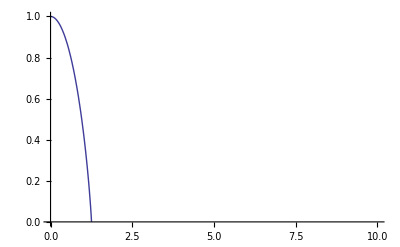

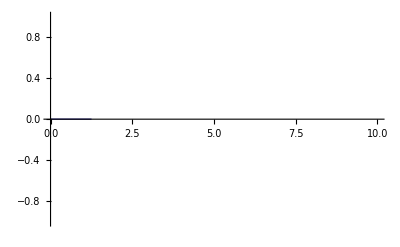

```mathematica
Plot[Evaluate[Re[sols[[1,1,2]]/.{A->1,C[1]->1,C[2]->0}]//N],{t,0,10}]
Plot[Evaluate[Im[sols[[1,1,2]]/.{A->1,C[1]->1,C[2]->0}]//N],{t,0,10}]
```

```mathematica
sols[[1,1,2]]/.{A->1,C[1]->1,C[2]->0,t->I}//N
```

0.443299

```mathematica
InverseErf[-√(2/π)]^2//N
```

0.813511